```mathematica
ClearAll["Global`*"];
NotebookFind[SelectedNotebook[],"Output",All,CellStyle];FrontEndExecute[FrontEndToken["Clear"]];
NotebookDelete@Cells@MessagesNotebook[];

Get[NotebookDirectory[]<>"H3Data.m"];
Get[NotebookDirectory[]<>"MData.m"];
Get[ParentDirectory[NotebookDirectory[]]<>"/Functions.m"];
```

Fusion rules

```mathematica
TableForm[Table[Sum[W[a,b][c]MNames[c],{c,obsM}],{a,obs},{b,obsM}],TableHeadings->{objNames[#]&/@obs,MNames[#]&/@obsM}]
```

| Γ | α Γ | α^2 Γ | Λ
1 | Γ | α Γ | α^2 Γ | Λ
α | α Γ | α^2 Γ | Γ | Λ
α^2 | α^2 Γ | Γ | α Γ | Λ
ρ | α Γ+α^2 Γ+Λ | Γ+α Γ+Λ | Γ+α^2 Γ+Λ | Γ+α Γ+α^2 Γ+Λ
α ρ | Γ+α^2 Γ+Λ | α Γ+α^2 Γ+Λ | Γ+α Γ+Λ | Γ+α Γ+α^2 Γ+Λ
α^2 ρ | Γ+α Γ+Λ | Γ+α^2 Γ+Λ | α Γ+α^2 Γ+Λ | Γ+α Γ+α^2 Γ+Λ

#### Dimensions

```mathematica
dimM[#]&/@obsM
```

{√(4+√13),√(4+√13),√(4+√13),√(3/2 (5+√13))}

#### Unitary module category?

```mathematica
NpentagonMQ&&NunitaryMQ(*Being checked numerically, can check exactly by removing leading 'N'*)
```

True

#### Visualizations

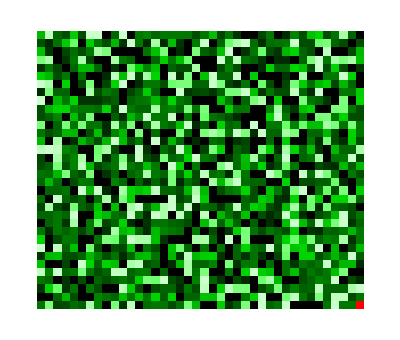

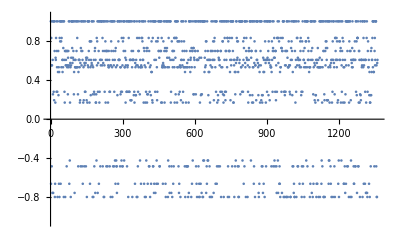

```mathematica
ArrayPlot[ArrayReshape[RandomSample[(Ls+1)/2],{34,40},∞],ColorFunction-> (If[#<∞,Blend[{White,Green,Black},#],Red]&),Frame->False,ColorFunctionScaling->False](*∞ turns up only to make the figure a nice shape!*)
ListPlot[RandomSample[Ls],PlotRange->{-1.05,1.05}]
```

```mathematica
Lblk[3,3,3][3]//MatrixForm
```

(Root0.482Root[1-5 #1^2+3 #1^4&,3]0.48208725429739563 | Root0.482Root[1-5 #1^2+3 #1^4&,3]0.48208725429739563 | Root0.482Root[1-5 #1^2+3 #1^4&,3]0.48208725429739563 | Root0.550Root[-1+3 #1^2+#1^4&,2]0.5502505227003375
-1/3 √(-2+√13) | 1/6 √(7+√13+√(-210+78 √13)) | Root0.245Root[1-19 #1^2+43 #1^4-63 #1^6+81 #1^8&,3]0.24526555058874314 | Root-0.482Root[1-5 #1^2+3 #1^4&,2]-0.48208725429739563
Root0.245Root[1-19 #1^2+43 #1^4-63 #1^6+81 #1^8&,3]0.24526555058874314 | -1/3 √(-2+√13) | 1/6 √(7+√13+√(-210+78 √13)) | Root-0.482Root[1-5 #1^2+3 #1^4&,2]-0.48208725429739563
1/6 √(7+√13+√(-210+78 √13)) | Root0.245Root[1-19 #1^2+43 #1^4-63 #1^6+81 #1^8&,3]0.24526555058874314 | -1/3 √(-2+√13) | Root-0.482Root[1-5 #1^2+3 #1^4&,2]-0.48208725429739563)